```mathematica
Clear["Global`*"]
```

```mathematica
x[t_]:=Sin[t]+1/4 Sin[10t]
```

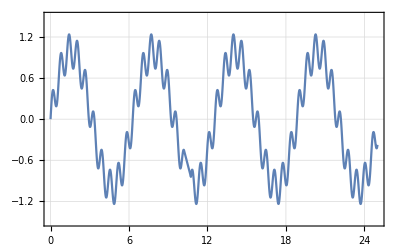

```mathematica
Plot[x[t],{t,0,25},PlotRange->{-1.5,1.5},Frame->True,GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}]
```

```mathematica
F1 = 1/(2π); F2=10/(2π);Fc = (F1+F2)/2;
```

```mathematica
wp=2π(Fc-8/10 Fc);ws= 2π Fc;ap=50;as=2;
```

```mathematica
tf=ButterworthFilterModel[{"Lowpass",{wp,ws},{as,ap}}];
```

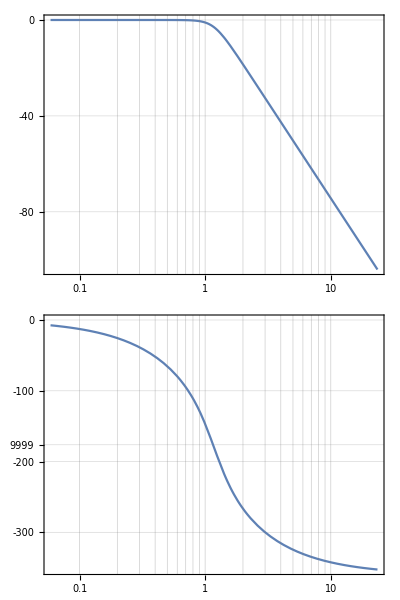

```mathematica
BodePlot[tf,GridLines->Automatic]
```

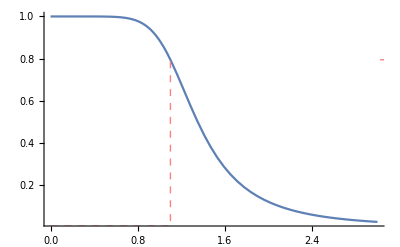

```mathematica
gp=10^(-ap/20);gs=10^(-as/20);
Plot[Abs[tf[I*ω]],{ω,0,3},PlotRange->All,Epilog->{Pink,Dashed,Line[{{0,gp},{wp,gp},{wp,gs}}],Line[{{ws,gp},{ws,gs},{3.,gs}}]}]
```

```mathematica
input = x[t]UnitStep[t];
response = OutputResponse[tf,input,{t,0,60}];
```

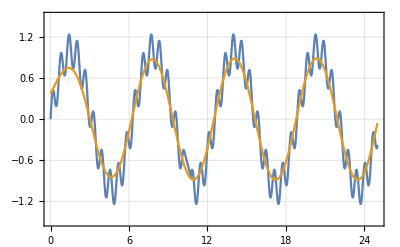

```mathematica
w=wp;
Plot[Evaluate[{input,response/.t->(t-Arg[tf[N[I w]]]/w)}],{t,0,25},PlotRange->{-1.5,1.5},Frame->True,GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}]
```

```mathematica
wp=2π(Fc+8/10 Fc);ws= 2π Fc;as=50;ap=2;
```

```mathematica
tf=ButterworthFilterModel[{"Highpass",{ws,wp},{as,ap}}];
```

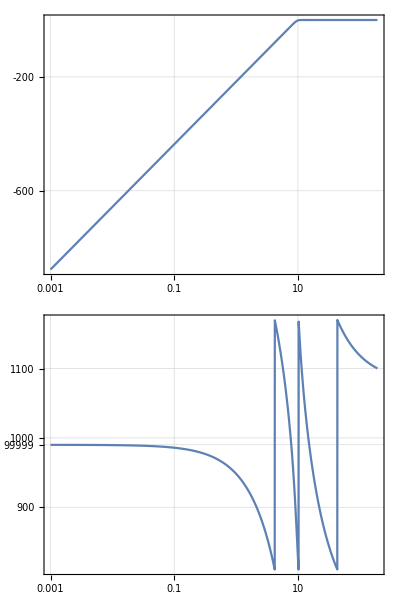

```mathematica
BodePlot[tf,GridLines->Automatic]
```

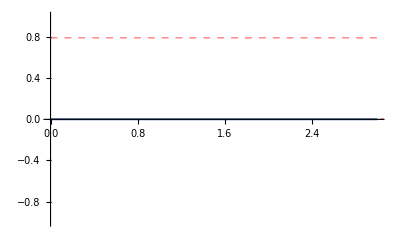

```mathematica
gp=10^(-ap/20);gs=10^(-as/20);
Plot[Abs[tf[I*ω]]/.ω->2π f,{f,0,3},PlotRange->All,Epilog->{Pink,Dashed,Line[{{0,gp},{wp,gp},{wp,gs}}],Line[{{ws,gp},{ws,gs},{3.,gs}}]}]
```

```mathematica
input = x[t]UnitStep[t];
response = OutputResponse[tf,input,{t,0,60}];
```

NDSolve::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

```mathematica
w=wp;
Plot[Evaluate[{input,response/.t->(t-Arg[tf[N[I w]]]/w)}],{t,0,25},PlotRange->{-1.5,1.5},Frame->True,GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}]
```